# Marcus rate expression for Onodera2 solvent

## Numerical integration of the flux

## Constants

### Unit conversions

```mathematica
au2kcal=627.5095;
kcal2au=1/au2kcal;
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;
au2cm=1/cm2au;
au2ps=2.4189 10^-5;
fs2ps=10^-3;
ps2au=1/au2ps;
```

### Universal constants

```mathematica
hbar=1;
kb=3.16683 10^-6;
```

## Dielectric function

```mathematica
ϵD[ω_]:=ϵi+(ϵ1-ϵi)/(1-ⅈ ω τ2) + (ϵ0-ϵ1)/(1-ⅈ ω τ1);
```

```mathematica
imϵD[ω_]:=((ϵ1-ϵi)ω τ2)/(1+ ω^2 τ2^2) + ((ϵ0-ϵ1) ω τ1)/(1+ ω^2 τ1^2);
```

```mathematica
reϵD[ω_]:=ϵi+(ϵ1-ϵi)/(1+ ω^2 τ2^2) + (ϵ0-ϵ1)/(1+ ω^2 τ1^2);
```

```mathematica
ϵDabs2[ω_]:=(reϵD[ω])^2+(imϵD[ω])^2;
```

```mathematica
ξ[ω_]:=imϵD[ω]/ϵDabs2[ω];
```

```mathematica
Series[(Cosh[1/2 x-(I x t)/(β ℏ)]-Cosh[1/2 x])/Sinh[1/2 x],{x,0,3}];
```

```mathematica
G[ω_] =ξ[ω]((-t^2-ⅈ t β ℏ)/(β ℏ ω));
```

```mathematica
Simplify[ξ[ω]]
```

(ω (-ϵi τ2 (1+τ1^2 ω^2)+ϵ0 (τ1+τ1 τ2^2 ω^2)+ϵ1 (τ2+τ1^2 τ2 ω^2-τ1 (1+τ2^2 ω^2))))/(2 ϵ0 (ϵ1-ϵi) (τ1-τ2) τ2 ω^2+ϵ0^2 (1+τ2^2 ω^2)+ω^2 (ϵ1^2 (τ1-τ2)^2+2 ϵ1 ϵi (τ1-τ2) τ2+ϵi^2 τ2^2 (1+τ1^2 ω^2)))

```mathematica
ϵ0 = 79.0;
ϵi = 1.75;
τO = 0.02;
```

```mathematica
τD = 11.5;
```

```mathematica
β = 1/(kb*298);
ℏ = hbar;
f0 = 12.696;
```

```mathematica
λ = 23.4645;
T = 298;
ϵ1 = 78;
τ1 = .005;
```

```mathematica
τ2 = 5.7;
```

```mathematica
F[ω_] =(  (f0 λ)/(4 π^2 ℏ))ξ[ω]*(1/(β ℏ ω));
```

```mathematica
FI = Integrate[F[ω],{ω,-∞,∞}]
```

0.0125009+0. ⅈ

## Flux

```mathematica
g[t_]:=Exp[-ⅈ/ℏ(G+λ)t+ⅈ/ℏ λ Abs[t]- FI * (-t^2-ⅈ Abs[t] β ℏ)];
```

```mathematica
fluxOnodera[G_, λ_,τ1_,τ2_,ϵi_,ϵ0_,ϵ1_,t_,T_] := Module[{β,hbar,f0,FI},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
f0 =  (4 π ϵ0 ϵi)/(ϵ0-ϵi);
FI = Re[NIntegrate[(  (f0 λ)/(4 π^2 hbar))(ω (-ϵi τ2 (1+τ1^2 ω^2)+ϵ0 (τ1+τ1 τ2^2 ω^2)+ϵ1 (τ2+τ1^2 τ2 ω^2-τ1 (1+τ2^2 ω^2))))/(2 ϵ0 (ϵ1-ϵi) (τ1-τ2) τ2 ω^2+ϵ0^2 (1+τ2^2 ω^2)+ω^2 (ϵ1^2 (τ1-τ2)^2+2 ϵ1 ϵi (τ1-τ2) τ2+ϵi^2 τ2^2 (1+τ1^2 ω^2)))*(1/(β hbar ω)),{ω,-∞,∞}]];
Exp[-ⅈ/hbar(G+λ)t+ⅈ/hbar λ Abs[t]]*Exp[FI*(-t^2-ⅈ Abs[t] β hbar)]
];
```

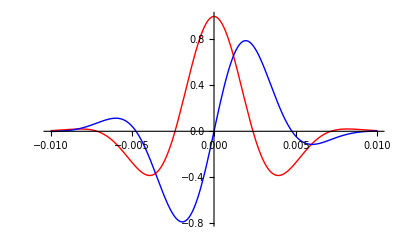

```mathematica
λλ=20.0;
dG=-30;
Temp=298;
τO=0.5;
ϵ1 = 84.0;
ϵ0 = 85.7;
ϵi = 1;
τO = .009;
τ1 = 0.01;
τ2 = 5.68;
Plot[{Re[fluxOnodera[dG,λλ,τ1,τ2,ϵi,ϵ0,ϵ1,t,Temp]],Im[fluxOnodera[dG,λλ,τ1,τ2,ϵi,ϵ0,ϵ1,t,Temp]]},{t,-0.01,0.01},PlotRange->All,PlotStyle->{Red,Blue}]
```

## Nonadiabatic rate

```mathematica
V=0.1;
```

```mathematica
Marcusrate[V_,G_,λ_,T_]:=Module[{β,hbar},
β=1/(kb T au2kcal);
hbar=au2kcal au2ps;
(2π)/hbar V^2 √(β/(4π λ))Exp[-β(G+λ)^2/(4λ)]
];
```

```mathematica
rateOnodera[V_,G_,λ_,τ1_,τ2_,ϵi_,ϵ0_,ϵ1_,T_] := Module[{β,hbar,g,integral,t,f0},
β = 1/(kb T au2kcal);
hbar = au2kcal au2ps;
f0 =  (4 π ϵ0 ϵi)/(ϵ0-ϵi);
FI = NIntegrate[(  (f0 λ)/(4 π^2 hbar))(ω (-ϵi τ2 (1+τ1^2 ω^2)+ϵ0 (τ1+τ1 τ2^2 ω^2)+ϵ1 (τ2+τ1^2 τ2 ω^2-τ1 (1+τ2^2 ω^2))))/(2 ϵ0 (ϵ1-ϵi) (τ1-τ2) τ2 ω^2+ϵ0^2 (1+τ2^2 ω^2)+ω^2 (ϵ1^2 (τ1-τ2)^2+2 ϵ1 ϵi (τ1-τ2) τ2+ϵi^2 τ2^2 (1+τ1^2 ω^2)))*(1/(β hbar ω)),{ω,-∞,∞}];
integral = NIntegrate[Exp[-ⅈ/hbar(G+λ)t+ⅈ/hbar λ Abs[t]]*Exp[FI*(-t^2-ⅈ Abs[t] β hbar)],{t,-∞,∞}];
V^2/hbar^2 Re[integral] 
];
```

```mathematica
λλ=20.0;
dG=-25;
τD=8.5;
Temp=298;
V = 0.1;
τL = 0.1;
```

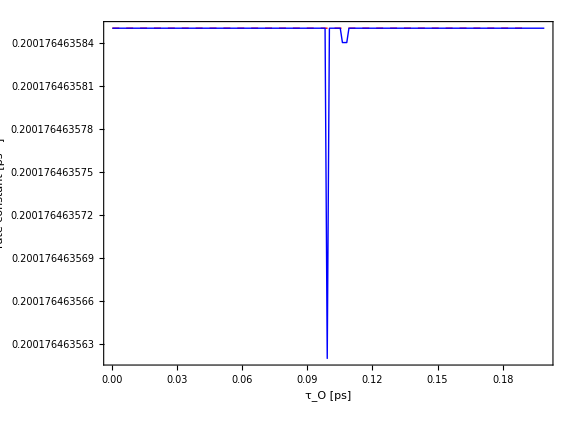

```mathematica
ListLinePlot[{Table[{τ1,Marcusrate[V,dG,λλ,Temp]},{τ1,0.0002,0.2,0.01}],Table[{τ1,rateOnodera[V,dG,λλ,τ1,τ2,ϵi,ϵ0,ϵ1,298]},{τ1,0.0002,0.2,0.001}]},PlotRange->All,PlotStyle->{{Red,Thick,Dashed},{Blue,Thick}},Axes->False,Frame->True,BaseStyle->{FontSize->24},FrameStyle->Thickness[0.0018],FrameLabel->{"τ_O [ps]","rate constant [ps^-1]"},AspectRatio->0.75,ImageSize->Large]
```

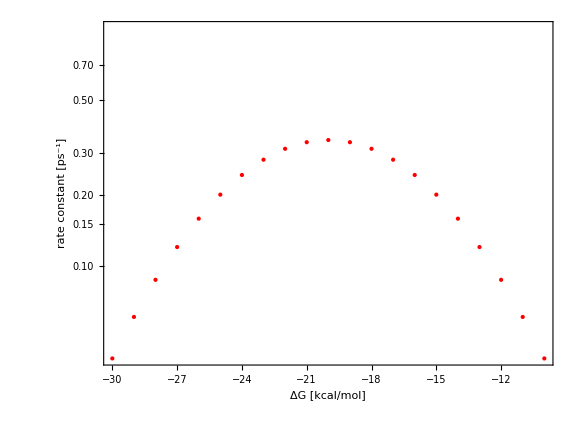

```mathematica
ListLogPlot[{Table[{G,Marcusrate[V,G,λλ,0.01,Temp]},{G,-30,-10,1}],Table[{G,rateDebye[V,G,λλ,0.01,Temp]},{G,-30,-10,1}]},PlotStyle->{Red,Blue},Axes->False,Frame->True,FrameLabel->{"ΔG [kcal/mol]","rate constant [ps^-1]"},AspectRatio->0.75,ImageSize->Large]
```